```mathematica
(*
e[x]_here = e[1][x]_{Lagrangian approach}
*)
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
ϵ[1]=1;
```

```mathematica
ass={ψ[x]∈Reals,ν[x]>0};
```

```mathematica
e[x_]:=ν[x]{Cos[ψ[x]],-Sin[ψ[x]]}
```

```mathematica
n[x_]:={-e[x][[2]],e[x][[1]]}/Norm[e[x]]
```

```mathematica
g[x_]:=Simplify[{{e[x].e[x]}},Assumptions->ass]
```

```mathematica
sqrtdetg[x_]:=Sqrt[Det[g[x]]]
```

```mathematica
gc[x_]:=Inverse[g[x]]
```

```mathematica
FullSimplify[{{-n'[x].e[x]}},Assumptions->ass]
```

{{-ν[x] ψ'[x]}}

```mathematica
b[x_]:={{-ν[x] ψ'[x]}}
```

```mathematica
1/2FullSimplify[Sum[gc[x][[i,j]]b[x][[j,i]],{i,1,1},{j,1,1}],Assumptions->ass]
```

-ψ'[x]/(2 ν[x])

```mathematica
H[x_]:=-ψ'[x]/(2 ν[x])
```

```mathematica
K[x_]:=0
```

```mathematica
Γ[x_]:=ResourceFunction["ChristoffelSymbol"][g[x],{x}] //FullSimplify
```

```mathematica
Γ[x]
```

{{{ν'[x]/ν[x]}}}

```mathematica
(* \Nabla_k f_i*)
```

```mathematica
Nablaf[f_][i_,k_][x_]:=Derivative[ϵ[k]][f[i]][x]-Sum[f[j][x] Γ[x][[j,i,k]],{j,1,1}]
```

```mathematica
dH[1][x_]:=H'[x]
```

```mathematica
FullSimplify[Sum[gc[x][[i,j]]Nablaf[dH][i,j][x],{i,1,1},{j,1,1}],Assumptions->ass]
```

(-3 ν'[x]^2 ψ'[x]+3 ν[x] ν'[x] ψ''[x]+ν[x] (ψ'[x] ν''[x]-ν[x] ψ^(3)[x]))/(2 ν[x]^5)

```mathematica
NabNabH[x_]:=(-3 ν'[x]^2 ψ'[x]+3 ν[x] ν'[x] ψ''[x]+ν[x] (ψ'[x] ν''[x]-ν[x] Derivative[3][ψ][x]))/(2 ν[x]^5)
```

```mathematica
eqψ=FullSimplify[{2 κ(2H[x](H[x]^2-K[x])+NabNabH[x])-2 σ[x]H[x]==0},Assumptions->ass]
```

{2 ν[x] (ψ'[x] (ν[x]^3 σ[x]+κ ν''[x])+3 κ ν'[x] ψ''[x])==6 κ ν'[x]^2 ψ'[x]+κ ν[x]^2 (ψ'[x]^3+2 ψ^(3)[x])}

```mathematica
eqX={X1'[x]==ν[x] Cos[ψ[x]],X2'[x]==-ν[x] Sin[ψ[x]]}
```

{X1'[x]==Cos[ψ[x]] ν[x],X2'[x]==-Sin[ψ[x]] ν[x]}

```mathematica
eqν={ν''[x]==0}
```

{ν''[x]==0}

```mathematica
bcs={ψ[xmin]==ψmin,ψ[xmax]==ψmax,X1[xmin]==X1min,X2[xmin]==X2min,X1[xmax]==X1max,X2[xmax]==X2max,ν[xmin]==νmin};
```

```mathematica
σ[x_]:=σc
(*fix the gauge*)
```

```mathematica
eqψ
```

{2 ν[x] (ψ'[x] (σc ν[x]^3+κ ν''[x])+3 κ ν'[x] ψ''[x])==6 κ ν'[x]^2 ψ'[x]+κ ν[x]^2 (ψ'[x]^3+2 ψ^(3)[x])}

```mathematica
(*parameters*)
```

```mathematica
κ=1;
σc=1;
xmin=1;
xmax=3;
ψmin=-1/2;
ψmax =2.5;
X1min=0;
X2min=0;
X1max=1;
X2max=1;
νmin=1;
```

```mathematica
s=NDSolve[Flatten[{eqψ,eqX,eqν, bcs}],{ψ,X1,X2,ν},{x,xmin,xmax}][[1]]
```

{ψ→InterpolatingFunction[…],X1→InterpolatingFunction[…],X2→InterpolatingFunction[…],ν→InterpolatingFunction[…]}

```mathematica
ν[xmin]/.s
ν[xmax]/.s
```

1.

```mathematica
2.7794766737521934
```

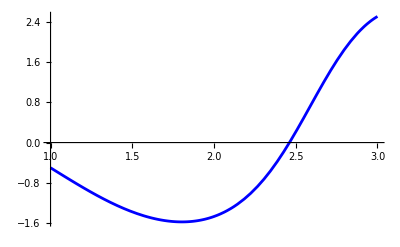

```mathematica
plotψexact=Plot[ψ[x]/.s,{x,xmin,xmax},PlotStyle->Blue]
```

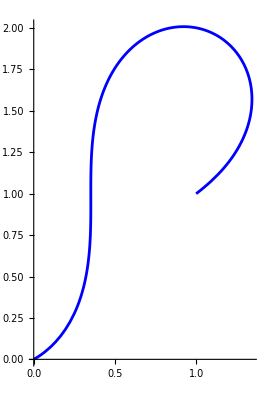

```mathematica
plotXexact=ParametricPlot[{X1[x],X2[x]}/.s,{x,xmin,xmax},PlotStyle->Blue]
```

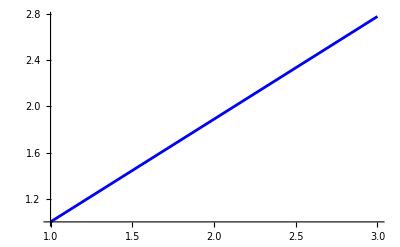

```mathematica
Plot[ν[x]/.s,{x,xmin,xmax},PlotStyle->Blue]
```

```mathematica
(*check FE solution*)
```

```mathematica
(*check ψ*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/lagrangian_approach/one_dimension/solution/nodal_values/psi.csv"];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

{{3.,2.5},{2.9,-1.16787},{2.8,-5.33966},{2.7,-9.37326},{2.6,-13.4018},{2.5,-17.417},{2.4,-22.5109},{2.3,-17.3183},{2.2,-13.2633},{2.1,-9.21339},{2.,-5.15701},{1.9,-1.09877},{1.8,2.95834},{1.7,7.00612},{1.6,11.0207},{1.5,15.2302},{1.4,16.3384},{1.3,11.7328},{1.2,7.65928},{1.1,3.64023},{1.,-0.5}}

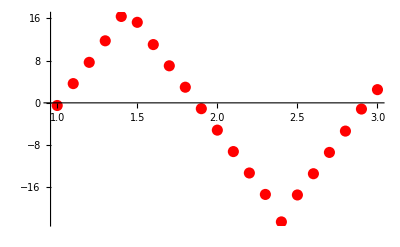

```mathematica
plotψnum=ListPlot[t,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

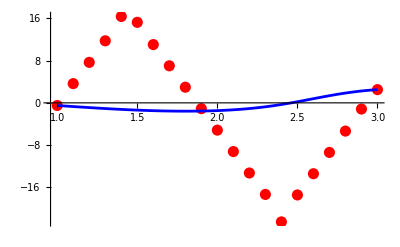

```mathematica
Show[plotψnum,plotψexact]
```

```mathematica
(*check X*)
```

```mathematica
tX=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/lagrangian_approach/one_dimension/solution/nodal_values/X.csv"];
tX=Table[{tX[[i,1]],tX[[i,2]]},{i,2,Length[tX]}]
```

{{1.,1.},{0.903707,0.814149},{0.862741,0.97816},{0.874631,0.785852},{0.84626,0.936168},{0.837032,0.75069},{0.805544,0.889156},{0.714115,0.992867},{0.767392,0.835678},{0.661141,0.931185},{0.723255,0.790574},{0.599243,0.854453},{0.666532,0.731118},{0.525461,0.759157},{0.584264,0.651151},{0.43636,0.655958},{0.458335,0.468081},{0.289459,0.437352},{0.283556,0.299335},{0.0961806,0.209372},{0.,0.}}

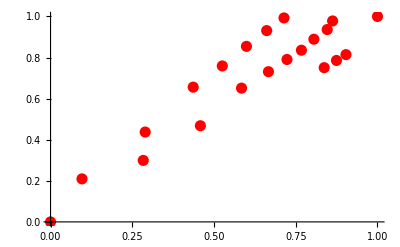

```mathematica
plotXnum=ListPlot[tX,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

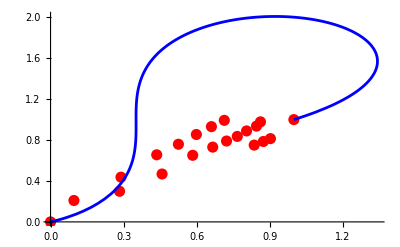

```mathematica
Show[plotXnum,plotXexact,PlotRange->Full]
```

```mathematica
(*plot the normal to the manifold n*)
```

```mathematica
(*tn=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/lagrangian_approach/one_dimension/solution/nodal_values/n.csv"];
tn=Table[{tn[[i,1]],tn[[i,2]]},{i,2,Length[tn]}]*)
```

```mathematica
(*plotn=Graphics[{Red,Table[Arrow[{{tX[[i,1]],tX[[i,2]]},{tX[[i,1]]+0.1*tn[[i,1]],tX[[i,2]]+0.1*tn[[i,2]]}}],{i,1,Length[t]}]},Frame->True,AspectRatio->1,PlotRange->All]*)
```